## Vector addition and vector (and scalar) sign figures: VectorsWithOppositeOrientationFig1.eps, vectorAdditionFig1.eps, scalarOrientationFig1.eps

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

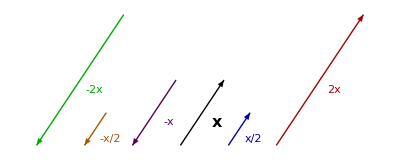

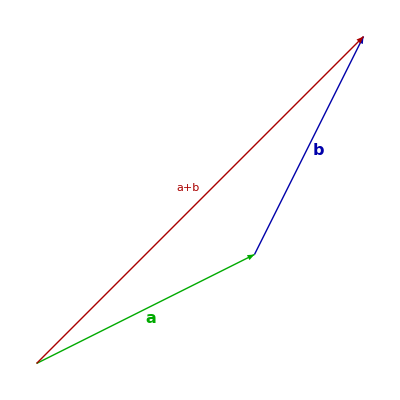

```mathematica
ClearAll[e1,e2,bold, fs, o]

bold = Style[ #, Bold] &;
fs:= Style[ #, FontSize -> 16 ]&;

(*{e1,e2,e3}= IdentityMatrix[3];*)
{e1,e2}= IdentityMatrix[2];
o = {0,0};

ClearAll[clk, ctr, rp, rn]
ctr =RotationTransform[Pi/2];
clk =RotationTransform[-Pi/2];
rp = ctr[#//Normalize] &;
rn = clk[#//Normalize] &;


p4=Module[{x0,x1,h0,h1,d0,d1,n0,n1,nh0,nh1,hd0,nd1, s, of},
x0=o;
of= 0.8;
s = 2.2 e1;
x1=2(e1+1.5 e2);
(*half*)
h0=x0+s;
h1=x1/2+s;
(*double*)
d0=x0+2 s;
d1=2 x1+2 s;
(*negated*)
n0=x1-s;
n1=x0-s;
(*half negated*)
nh0=x1/2-2 s;
nh1=x0-2 s;
(*double negated*)
nd0=2 x1-3 s;
nd1=x0-3 s;
Graphics[{
Thick,
Arrowheads[0.05],
Black,Arrow[{x0,x1}],
Text["x"//bold//fs,(x0+x1)/2-of rp[x1-x0]],
Blue//Darker,Arrow[{h0,h1}],
Text[("x"//bold//fs)/("2" //fs),(h0+h1)/2-of rp[h1-h0]],
Red//Darker,Arrow[{d0,d1}],
Text[Row[{"2"//fs,"x"//bold//fs}],(d0+d1)/2-of rp[d1-d0]],
Purple//Darker,Arrow[{n0,n1}],
Text[Row[{"-"//fs,"x"//bold//fs}],(n0+n1)/2+of rp[n1-n0]], 
Orange//Darker,Arrow[{nh0,nh1}],
Text[Row[{"-"//fs,"x"//bold//fs}]/("2" //fs),(nh0+nh1)/2+of rp[nh1-nh0]], 
Green//Darker,Arrow[{nd0,nd1}],
Text[Row[{"-2"//fs, "x"//bold//fs}],(nd0+nd1)/2+of rp[nd1-nd0]]
}]]


p2 = Module[{v1,v2,vs},
v1 = e1 + 0.5e2;
v2 = 0.5 e1 + e2;
vs = v1 + v2;

Graphics[ {
Thick,
Arrowheads[0.05],
Green // Darker,
Arrow[{o,v1}],
Text["a"//bold//fs, v1/2+0.05 rn[v1] ],
Blue // Darker,
Arrow[{v1,vs} ],
Text["b"//bold//fs, v1 + v2/2+0.05 rn[v2]],
Red // Darker,
Arrow[{o,vs} ],
Text[Row[{
"a"//bold//fs,
"+" // fs,
"b"//bold//fs}]
, vs/2 + 0.08rp[vs]]
}]
]
```

```mathematica
peeters`exportForLatex["VectorsWithOppositeOrientationFig1", p4] (* was p1 *)
peeters`exportForLatex["vectorAdditionFig1", p2]
```

{VectorsWithOppositeOrientationFig1.eps,VectorsWithOppositeOrientationFig1pn.png}

{vectorAdditionFig1.eps,vectorAdditionFig1pn.png}

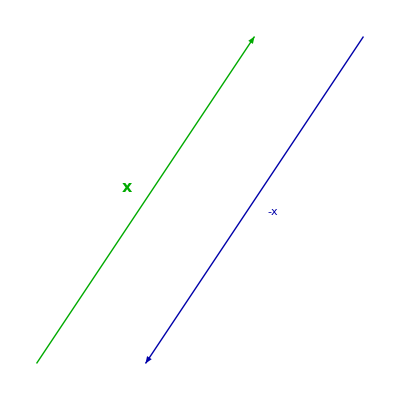

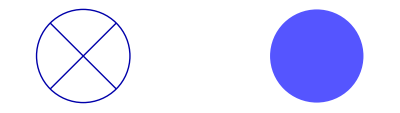

```mathematica
p1 = Module[{x0,x1,y0, y1},
x0 = o;
x1 = e1+1.5e2;
y0 = 1.5 e1+1.5e2;
y1 = e1/2;
Graphics[ {
Thick,
Arrowheads[0.05],
Green // Darker,
Arrow[{x0,x1}],
Text["x"//bold//fs,  (x0+x1)/2 + 0.1 rp[x1-x0]],
Blue // Darker,
Arrow[{y0, y1} ],
Text[Row[{"-"//fs,"x"//bold//fs}],  (y0+y1)/2 + 0.1 rp[y1-y0]]
}]
]



p3 = Module[{p1, p2,r},
r = 0.01;
p1 = r(e1+e2)/Sqrt[2];
p2 = r(e1-e2) /Sqrt[2];
Graphics[ {
Thick,
Blue//Darker,
Circle[o,r],

Line[{-p1, p1}],
Line[{-p2,p2}],
Blue// Lighter,
Disk[0.05 e1,r]
}]
]
```

```mathematica
peeters`exportForLatex["scalarOrientationFig1", p3]
```

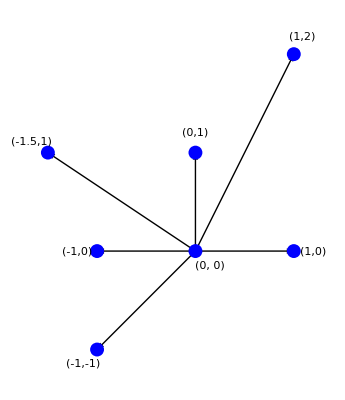

```mathematica
p5 = Module[{x},
x = {{1,0}, {1,2}, {0,1}, {-1.5,1},{-1,-1}, {-1,0}};
{ 
{
Thick,
Arrowheads[0.05]
}
,Arrow[{o,#}]&/@ x
, Text[Row[fs[#] &/@{"(", #[[1]], ",", #[[2]], ")"}],# + 0.2 Normalize[#]]&/@ x
,Blue
,PointSize -> 0.025
,Point[#]&/@ x
,Point[o]
, Black
, Text[Row[fs[#] &/@{"(0, 0)"}],0.15{1,-1}]
} // Flatten // Graphics

]
```

```mathematica
peeters`exportForLatex["coordinateRepresentationFig1", p5]
```

{coordinateRepresentationFig1.eps,coordinateRepresentationFig1pn.png}